Gabriella Adam

```mathematica
Math 9 Final Project
```

## Daily Increase in New COVID - 19 Cases in the United States

To show the magnitude of new COVID - 19 cases in each state, this section will be dedicated to displaying a map of the continental United States with each state colored according to how many COVID tests for that day returned positive in relation to the max daily increase for that particular state.

```mathematica
(*From The COVID Tracking Project, I've imported "data for all states". URL: https://covidtracking.com/data/download*)
```

```mathematica
states = Import["C:\\Users\\adamg\\OneDrive\\Desktop\\Math 9\\all-states-history.csv", "Dataset", HeaderLines -> 1];
```

```mathematica
(*The column "positiveIncrease" is defined as the number of confirmed and probable COVID cases that have increased based on the previous day.*)
columns = Normal[Keys[states[[1]]]];
```

```mathematica
positiveIn = states[All, {"date","state","positiveIncrease"}];
```

```mathematica
positiveIn[1;;100]
```

```mathematica
(*Since I am only looking at the continental United States, I will remove all of the rows that contain "AK" for Alaska and "HI" for Hawaii*)
continentalDS = DeleteCases[positiveIn, x_/; StringContainsQ[x["state"],"AK"] ||StringContainsQ[x["state"],"HI"]];
```

```mathematica
continentalDS[1;;100]
```

```mathematica
Head[positiveIn[1,"date"]] (*String, must convert date column from string to DateObject*)
```

String

```mathematica
newContinentalDS= continentalDS[All, {"date" -> (DateObject@#&)}]
```

Dataset[<>]

```mathematica
Head[newContinentalDS[1,"date"]](*DateObject*)
```

DateObject

```mathematica
Goal: Get the population for each unique state and create an association between state and population
```

```mathematica
listStates = Normal[DeleteDuplicates[newContinentalDS[All, "state"]]]; (*all unique states found in dataset*)
```

```mathematica
Length[listStates] (*54, meaning US territories are included. Since I already removed 2 US states, there must be 48 states in total.*)
```

54

```mathematica
entityListStates = EntityList[EntityClass["AdministrativeDivision","USStatesAllStates"]]; (*entities of all 50 states*)
```

```mathematica
akEntity = Entity["AdministrativeDivision",{"Alaska","UnitedStates"}];
```

```mathematica
hiEntity = Entity["AdministrativeDivision",{"Hawaii","UnitedStates"}];
```

```mathematica
validListStates = DeleteCases[entityListStates, akEntity | hiEntity];(*Remove Alaska and Hawaii from list of entities*)
```

```mathematica
Length[validListStates] (*48 states*)
```

48

```mathematica
listAbbrevS = Table[i[EntityProperty["AdministrativeDivision","StateAbbreviation"]],{i,validListStates}]; (*abbreviations of all 48 states*)
```

```mathematica
statesDataset = DeleteCases[newContinentalDS, x_/; !MemberQ[listAbbrevS,x["state"]]]; (*new dataset containing only continental US states*)
```

```mathematica
Length[Normal[DeleteDuplicates[statesDataset[All,"state"]]]](*48 unique states recorded in dataset*)
```

48

```mathematica
listStatePopulation = Table[i -> Max[statesDataset[Select[#["state"] == i&], "positiveIncrease"]], {i,listAbbrevS}] (*List in the form of state -> max daily increase*)
```

{AL→3928,AZ→10322,AR→2789,CA→20759,CO→6439,CT→5271,DE→758,FL→16795,GA→4813,ID→1997,IL→15415,IN→8460,IA→4381,KS→7526,KY→5616,LA→5326,ME→346,MD→2910,MA→6675,MI→17368,MN→9022,MS→2457,MO→6346,MT→1642,NE→3440,NV→3159,NH→772,NJ→4793,NM→3665,NY→11571,NC→8008,ND→2270,OH→17065,OK→6257,OR→1674,PA→11406,RI→1717,SC→2665,SD→2138,TN→7975,TX→17820,UT→6142,VT→181,VA→3242,WA→6277,WV→1153,WI→8510,WY→1262}

```mathematica
assocSP = Association[listStatePopulation] (*Association in the form of state -> max daily increase*)
```

<|AL→3928,AZ→10322,AR→2789,CA→20759,CO→6439,CT→5271,DE→758,FL→16795,GA→4813,ID→1997,IL→15415,IN→8460,IA→4381,KS→7526,KY→5616,LA→5326,ME→346,MD→2910,MA→6675,MI→17368,MN→9022,MS→2457,MO→6346,MT→1642,NE→3440,NV→3159,NH→772,NJ→4793,NM→3665,NY→11571,NC→8008,ND→2270,OH→17065,OK→6257,OR→1674,PA→11406,RI→1717,SC→2665,SD→2138,TN→7975,TX→17820,UT→6142,VT→181,VA→3242,WA→6277,WV→1153,WI→8510,WY→1262|>

Goal: Create a map of the United States showing the magnitude of positive COVID cases in each state

```mathematica
listDates = Normal[DeleteDuplicates[statesDataset[All, "date"]]]; (*list of unique dates recorded in dataset*)
```

```mathematica
Length[listDates];(*313 unique dates recorded*)
```

```mathematica
Clear[getDateRows]; (*Takes in a DateObject, and returns all the data associated to it*)
getDateRows[d_] := Select[statesDataset, #["date"] == d&];
```

Testing: Get all of the recorded data underneath Thu 3 December 2020

```mathematica
getDateRows[listDates[[1]]]
```

Testing: Creating a map of the United States based on only one day’s worth of data for each state

```mathematica
testDataset = getDateRows[DateObject[{2020,11,1},"Day","Gregorian",-5.]](*Get all rows on Nov 1*)
```

```mathematica
testStates= Normal[testDataset[All,"state"]] (*{AL, AR...}*)
```

{AL,AR,AZ,CA,CO,CT,DE,FL,GA,IA,ID,IL,IN,KS,KY,LA,MA,MD,ME,MI,MN,MO,MS,MT,NC,ND,NE,NH,NJ,NM,NV,NY,OH,OK,OR,PA,RI,SC,SD,TN,TX,UT,VA,VT,WA,WI,WV,WY}

```mathematica
testValues = Table[testDataset[i, "positiveIncrease"], {i,Length[testDataset]}] (*{1700, 0...}*)
```

{1700,0,1527,4529,2560,0,175,4805,1192,2212,798,6980,2750,0,1423,1071,1131,864,47,0,2200,2349,340,694,2057,1127,1087,130,1743,742,716,2255,3303,1349,508,1909,480,1411,1332,754,4259,1854,1202,23,928,3553,423,425}

```mathematica
testValuesList = Table[{testStates[[i]],testValues[[i]]},{i,Length[testStates]}] (*List of lists, e.g. {{AL, 1700}, ...}*)
```

{{AL,1700},{AR,0},{AZ,1527},{CA,4529},{CO,2560},{CT,0},{DE,175},{FL,4805},{GA,1192},{IA,2212},{ID,798},{IL,6980},{IN,2750},{KS,0},{KY,1423},{LA,1071},{MA,1131},{MD,864},{ME,47},{MI,0},{MN,2200},{MO,2349},{MS,340},{MT,694},{NC,2057},{ND,1127},{NE,1087},{NH,130},{NJ,1743},{NM,742},{NV,716},{NY,2255},{OH,3303},{OK,1349},{OR,508},{PA,1909},{RI,480},{SC,1411},{SD,1332},{TN,754},{TX,4259},{UT,1854},{VA,1202},{VT,23},{WA,928},{WI,3553},{WV,423},{WY,425}}

```mathematica
testEntityKeys = Table[Interpreter["USState"][i],{i, testStates}] (*Entities of all the states shown in the dataset*)
```

{Alabama, United States,Arkansas, United States,Arizona, United States,California, United States,Colorado, United States,Connecticut, United States,Delaware, United States,Florida, United States,Georgia, United States,Iowa, United States,Idaho, United States,Illinois, United States,Indiana, United States,Kansas, United States,Kentucky, United States,Louisiana, United States,Massachusetts, United States,Maryland, United States,Maine, United States,Michigan, United States,Minnesota, United States,Missouri, United States,Mississippi, United States,Montana, United States,North Carolina, United States,North Dakota, United States,Nebraska, United States,New Hampshire, United States,New Jersey, United States,New Mexico, United States,Nevada, United States,New York, United States,Ohio, United States,Oklahoma, United States,Oregon, United States,Pennsylvania, United States,Rhode Island, United States,South Carolina, United States,South Dakota, United States,Tennessee, United States,Texas, United States,Utah, United States,Virginia, United States,Vermont, United States,Washington, United States,Wisconsin, United States,West Virginia, United States,Wyoming, United States}

```mathematica
Clear[color] (*Takes in the positiveIncrease number and state to retrieve the max positiveIncrease ever recorded for that state, and returns a color*)
color[x_,s_] := ColorData["Rainbow"][x/assocSP[s]];
```

```mathematica
testAssoc = AssociationThread[testEntityKeys, Table[color[i[[2]],i[[1]] ],{i, testValuesList}]] (*<|Alabama, United States -> color, ...|>*)
```

<|Alabama, United States→RGBColor[0.4246151283095723, 0.6983758228105906, 0.5482613808553972],Arkansas, United States→RGBColor[0.471412, 0.108766, 0.527016],Arizona, United States→RGBColor[0.24828829606665376, 0.275242861848479, 0.7863752528579733],California, United States→RGBColor[0.2548966026301845, 0.42278995096102895, 0.8094321966857749],Colorado, United States→RGBColor[0.38553606646994876, 0.6724083772324895, 0.6076281785991614],Connecticut, United States→RGBColor[0.471412, 0.108766, 0.527016],Delaware, United States→RGBColor[0.25937563588390505, 0.44827626385224273, 0.8066777598944591],Florida, United States→RGBColor[0.28910687049717176, 0.5437903292646621, 0.7662222956236976],Georgia, United States→RGBColor[0.26529765759401625, 0.4819733787658425, 0.8030359395387493],Iowa, United States→RGBColor[0.5208163371376399, 0.7310034311800959, 0.43423590641406073],Idaho, United States→RGBColor[0.3877802163244867, 0.673899580871307, 0.6042189874812218],Illinois, United States→RGBColor[0.4503087937074278, 0.7087233447940318, 0.515920271813169],Indiana, United States→RGBColor[0.3168827943262411, 0.5996781678486998, 0.7207823356973996],Kansas, United States→RGBColor[0.471412, 0.108766, 0.527016],Kentucky, United States→RGBColor[0.26827625356125356, 0.4920181566951567, 0.7991261595441596],Louisiana, United States→RGBColor[0.24887245888096132, 0.38851174765302293, 0.8131368182500939],Massachusetts, United States→RGBColor[0.24600119730337078, 0.3219811424719101, 0.8025211793258427],Maryland, United States→RGBColor[0.29599026391752575, 0.5608982350515463, 0.7553493463917527],Maine, United States→RGBColor[0.2495751676300578, 0.24894484393063585, 0.7772904971098266],Michigan, United States→RGBColor[0.471412, 0.108766, 0.527016],Minnesota, United States→RGBColor[0.26395249257370873, 0.47431920549767237, 0.8038631653735314],Missouri, United States→RGBColor[0.3562499319256225, 0.6503176939804601, 0.6529777245508983],Mississippi, United States→RGBColor[0.24930478144078144, 0.25447035327635326, 0.7791993064713064],Montana, United States→RGBColor[0.4133674689403167, 0.6909019232643118, 0.5653482168087698],North Carolina, United States→RGBColor[0.27049529670329675, 0.49753334065934063, 0.7956209780219781],North Dakota, United States→RGBColor[0.5087044008810573, 0.7283371418502202, 0.4463004105726872],Nebraska, United States→RGBColor[0.30896426511627906, 0.5894922465116279, 0.7344209395348837],New Hampshire, United States→RGBColor[0.24611229015544042, 0.31971089119170987, 0.8017369119170985],New Jersey, United States→RGBColor[0.3505763759649489, 0.6430195716670144, 0.6627496632589193],New Mexico, United States→RGBColor[0.24935444311050478, 0.3912543039563438, 0.8128404160982265],Nevada, United States→RGBColor[0.2578885210509655, 0.4398143767014878, 0.8075922795188352],New York, United States→RGBColor[0.24668404580416559, 0.37605937740903983, 0.814482609886786],Ohio, United States→RGBColor[0.24621509674772926, 0.3733909930266628, 0.8147709958980369],Oklahoma, United States→RGBColor[0.2539895646475947, 0.41762878056576636, 0.809989990890203],Oregon, United States→RGBColor[0.3001657897252091, 0.5712760382317801, 0.7487537216248507],Pennsylvania, United States→RGBColor[0.24622139505523408, 0.31748126494827283, 0.8009666785902156],Rhode Island, United States→RGBColor[0.28494271287128714, 0.5334407804309842, 0.7727999633080955],South Carolina, United States→RGBColor[0.5578289714821764, 0.736422922326454, 0.40199154446529084],South Dakota, United States→RGBColor[0.7019405650140318, 0.7426268447146867, 0.3010569101964453],Tennessee, United States→RGBColor[0.2801261381818182, 0.17285507636363637, 0.7181428290909091],Texas, United States→RGBColor[0.2622430038159372, 0.46459198024691356, 0.8049144365881034],Utah, United States→RGBColor[0.29914145815695214, 0.5687301764897427, 0.7503717469879518],Virginia, United States→RGBColor[0.35677752621838377, 0.6509963596545342, 0.6520690141887724],Vermont, United States→RGBColor[0.2505076243093923, 0.2298895138121547, 0.7707077569060773],Washington, United States→RGBColor[0.24829841389198662, 0.2750360978174287, 0.7863038253942967],Wisconsin, United States→RGBColor[0.40765594077555817, 0.6871066991774383, 0.5740248615746182],West Virginia, United States→RGBColor[0.3533818647007806, 0.6466283842150911, 0.6579175854293149],Wyoming, United States→RGBColor[0.32710354041204437, 0.6128255229793977, 0.7031784722662441]|>

```mathematica
GeoRegionValuePlot[testAssoc]
```

-Graphics-

```mathematica
Legended[GeoRegionValuePlot[testAssoc],BarLegend["Rainbow"]](*Code on how to add a legend to a GeoRegionValuePlot from @286 from Piazza*)
```

-Graphics-

Difficulty: Originally, I was planning on separating the dataset statesDataset based on months and then animating the change in COVID cases in each state for one entire month. However, the dataset is too large and it would be too time-consuming to do this. So, I’ve created a function that generates a GeoRegionValuePlot for one day’s worth of data in the United States, and then used another function to evaluate it for 7 consecutive days.

```mathematica
Clear[getDay] (*Takes in an integer for month and another integer for day. Returns a georegionvalueplot for that day*)
getDay[m_,d_] := ( day = DateObject[{2020,m,d}];
dayDataset = getDateRows[day];
dayStates = Normal[dayDataset[All, "state"]];
dayValues = Table[dayDataset[i,"positiveIncrease"],{i,Length[dayDataset]}];
       dayValuesList=Table[{dayStates[[i]],dayValues[[i]]},{i,Length[dayStates]}];
       dayEntityKeys=Table[Interpreter["USState"][i],{i,dayStates}];
       dayAssoc=AssociationThread[dayEntityKeys,Table[color[i[[2]],i[[1]]],{i,dayValuesList}]];
Legended[GeoRegionValuePlot[dayAssoc],BarLegend["Rainbow"]]
);
```

```mathematica
Clear[getWeek] (*Returns 7 different georegionvalueplots*)
getWeek[m_,d_] := Table[getDay[m,d+i],{i,0,6}];
```

Testing: Testing getWeek for November 1st, 2020 to November 7th, 2020

```mathematica
week = getWeek[11,1]; 
ListAnimate[week] (*Displays the US map and the magnitude of daily increases in positive cases for each state. Magnitude is shown through colors. Cool colors representing a small increase while warmer colors indicate a large increase in cases. Takes some time to run*)
```

## Increase in COVID Cases for a Single State

While a map of the entire United States allows someone to compare how states are doing with one another in terms of daily COVID case numbers, all of the different colors might be overwhelming to look at. Therefore, a line plot representing COVID cases for a particular state might be easier to understand.

```mathematica
Clear[makePlot]
makePlot[s_] := DateListPlot[statesDataset[Select[#["state"] == s&], {"date","positiveIncrease"}], PlotLabel -> s];
```

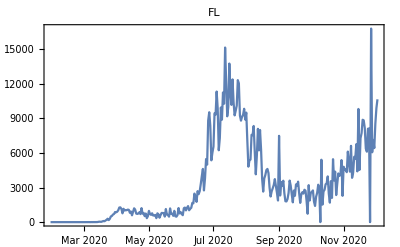

```mathematica
makePlot["FL"]
```

To view COVID cases for each state ...

```mathematica
statesAnimate = Table[makePlot[i],{i, listAbbrevS}];
```

```mathematica
ListAnimate[statesAnimate, 0.5]
```

## Hospitalizations, Viral Positive Cases, and Unemployment Claims

COVID has undoubtedly affect unemployement rates in the United States. To visualize COVID’s impact on the number of claims for unemployement, I will be comparing weekly unemployement cases to the number of current hospitalizations and viral positive cases in the United States as a whole.

```mathematica
unemployment = Import["C:\\Users\\adamg\\OneDrive\\Desktop\\Math 9\\ICSA.csv", "Dataset",HeaderLines -> 1]; (*Taken from the Economic Research Federal Reserve Bank of St. Louis. The data consists of weekly claims for unemploymennt from January 22nd, 2020 to November 28th, 2020. URL: https://fred.stlouisfed.org/series/ICSA#0*)
```

Goal: Display the data for unemployment claims for 2020

```mathematica
unemploymentDataset = unemployment[All, {"DATE" -> (DateObject@#&)}] (*Displays the date and the ICSA/initial claims for unemployment*)
```

```mathematica
unemploymentDataset = unemploymentDataset[All, <|#, "date" -> #["DATE"]|>&] (*Add new column named "date" to replace the original column "DATE"*)
```

```mathematica
unemploymentDataset = unemploymentDataset[All, {"date", "ICSA"}]
```

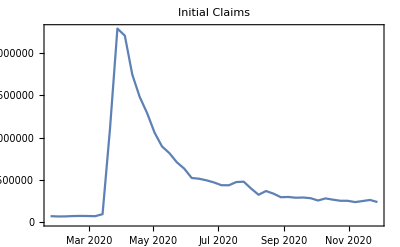

```mathematica
unemploymentPlot = DateListPlot[unemploymentDataset[All, {"date", "ICSA"}], PlotLabel -> "Initial Claims"](*Initial claims is defined as "a claim filed by an unemployed individual after a separation from an employer. The claim requests a determination of basic eligibility for the Unemployment Insurance program" *)
```

Goal: Create a dataset that contains current hospitalizations and number of viral positive cases for the entire United States for every day

```mathematica
statesHP= states[All, {"date", "state", "hospitalizedCurrently", "positiveCasesViral"}]
```

Dataset[<>]

```mathematica
statesHPDataset = statesHP[All, {"date" -> (DateObject@#&)}]
```

Dataset[<>]

```mathematica
statesHPDataset = DeleteCases[statesHPDataset, x_/; !MemberQ[listAbbrevS,x["state"]]]; (*Remove Alaska, Hawaii, and territories from the dataset*)
```

Difficulty: In the previous draft, summing up all of the hospitalization data for one day and the positive cases separately was too time-consuming. So, I combined the two datasets first before summing up the data.

```mathematica
combinedDataset = JoinAcross[unemploymentDataset, statesHPDataset, "date"]; (*date, ICSA, state, hospitalizedCurrently, positiveCasesViral*)
```

```mathematica
combinedDataset[1;;100]
```

```mathematica
combinedDSDates = Normal[DeleteDuplicates[combinedDataset[All, "date"]]](*All dates recorded in the combinedDataset*)
```

{Day: Sat 28 Nov 2020,Day: Sat 21 Nov 2020,Day: Sat 14 Nov 2020,Day: Sat 7 Nov 2020,Day: Sat 31 Oct 2020,Day: Sat 24 Oct 2020,Day: Sat 17 Oct 2020,Day: Sat 10 Oct 2020,Day: Sat 3 Oct 2020,Day: Sat 26 Sep 2020,Day: Sat 19 Sep 2020,Day: Sat 12 Sep 2020,Day: Sat 5 Sep 2020,Day: Sat 29 Aug 2020,Day: Sat 22 Aug 2020,Day: Sat 15 Aug 2020,Day: Sat 8 Aug 2020,Day: Sat 1 Aug 2020,Day: Sat 25 Jul 2020,Day: Sat 18 Jul 2020,Day: Sat 11 Jul 2020,Day: Sat 4 Jul 2020,Day: Sat 27 Jun 2020,Day: Sat 20 Jun 2020,Day: Sat 13 Jun 2020,Day: Sat 6 Jun 2020,Day: Sat 30 May 2020,Day: Sat 23 May 2020,Day: Sat 16 May 2020,Day: Sat 9 May 2020,Day: Sat 2 May 2020,Day: Sat 25 Apr 2020,Day: Sat 18 Apr 2020,Day: Sat 11 Apr 2020,Day: Sat 4 Apr 2020,Day: Sat 28 Mar 2020,Day: Sat 21 Mar 2020,Day: Sat 14 Mar 2020,Day: Sat 7 Mar 2020,Day: Sat 29 Feb 2020,Day: Sat 22 Feb 2020,Day: Sat 15 Feb 2020,Day: Sat 8 Feb 2020,Day: Sat 1 Feb 2020,Day: Sat 25 Jan 2020}

Difficulty: Below, I’ve created two different functions for computing the total hospitalizations for a particular day to compare which one is faster because it was initially time-consuming for my original function to go through the entire dataset.

Testing:

```mathematica
Clear[getNewDateRows]
getNewDateRows[d_] := Select[combinedDataset, #["date"] == d&];
```

```mathematica
Clear[testH1]
testH1[d_] := (
ds = getNewDateRows[d];
Total[ds[All, "hospitalizedCurrently"]]);
```

```mathematica
Clear[testH2]
testH2[d_] := Total[combinedDataset[Select[#["date"] == d&], "hospitalizedCurrently"]];
```

```mathematica
testDay = combinedDSDates[[1]]
```

Day: Sat 28 Nov 2020

```mathematica
Timing[testH1[testDay]]
```

{2.78125,90677}

```mathematica
Timing[testH2[testDay]] (*faster*)
```

{2.54688,90677}

Difficulty: Originally, when I applied the function to sum up all of the cases in each state for a particular day, it would return a number, a plus sign, and then another number after it for certain days (for example, 1000 + 2). After testing one day’s worth of data, I noticed that the number after the plus sign represents the number of rows with missing data. For example, if my output was 1000 + 2, that meant that two states did not report the number of hospitalizations or positive viral cases for that day. To deal with missing data, I only looked at rows that contained a number of 0 or above, as seen below in the final functions.

Final functions :

```mathematica
Clear[getTotalHDay]
getTotalHDay[d_] := Total[Cases[combinedDataset[Select[#["date"] == d&], "hospitalizedCurrently"], x_/; x ≥ 0]];
```

```mathematica
Clear[getTotalPDay] 
getTotalPDay[d_] := Total[Cases[combinedDataset[Select[#["date"] == d&], "positiveCasesViral"], x_/; x ≥ 0]];
```

```mathematica
listH = Table[getTotalHDay[i], {i,combinedDSDates}]
```

{90677,82234,68582,55066,46620,41295,36722,33920,29484,28885,28273,29823,32695,35638,39150,44079,49314,53715,58608,57173,51561,37929,32232,27694,28105,31379,35076,37920,42639,47958,53812,56770,57265,55540,30248,12394,1492,0,0,0,0,0,0,0,0}

```mathematica
listP = Table[getTotalPDay[i], {i,combinedDSDates}]
```

{11686183,10761027,9820554,9043494,8439640,7955088,7547365,7210276,6888545,6627084,6353946,6105978,5891626,5627237,5371266,5092440,4231874,3891078,3555056,3202288,2842877,2528252,2252640,2043734,1892420,1731069,1551702,1428942,1236391,1106199,960155,610100,473455,354134,221135,98202,24586,3853,508,18,0,0,0,0,0}

```mathematica
list = Table[ Association["date" -> combinedDSDates[[i]], "hospitalizations"->listH[[i]], "positiveViralCases" -> listP[[i]]], {i, Length[combinedDSDates]}]
```

{<|date→Day: Sat 28 Nov 2020,hospitalizations→90677,positiveViralCases→11686183|>,<|date→Day: Sat 21 Nov 2020,hospitalizations→82234,positiveViralCases→10761027|>,<|date→Day: Sat 14 Nov 2020,hospitalizations→68582,positiveViralCases→9820554|>,<|date→Day: Sat 7 Nov 2020,hospitalizations→55066,positiveViralCases→9043494|>,<|date→Day: Sat 31 Oct 2020,hospitalizations→46620,positiveViralCases→8439640|>,<|date→Day: Sat 24 Oct 2020,hospitalizations→41295,positiveViralCases→7955088|>,<|date→Day: Sat 17 Oct 2020,hospitalizations→36722,positiveViralCases→7547365|>,<|date→Day: Sat 10 Oct 2020,hospitalizations→33920,positiveViralCases→7210276|>,<|date→Day: Sat 3 Oct 2020,hospitalizations→29484,positiveViralCases→6888545|>,<|date→Day: Sat 26 Sep 2020,hospitalizations→28885,positiveViralCases→6627084|>,<|date→Day: Sat 19 Sep 2020,hospitalizations→28273,positiveViralCases→6353946|>,<|date→Day: Sat 12 Sep 2020,hospitalizations→29823,positiveViralCases→6105978|>,<|date→Day: Sat 5 Sep 2020,hospitalizations→32695,positiveViralCases→5891626|>,<|date→Day: Sat 29 Aug 2020,hospitalizations→35638,positiveViralCases→5627237|>,<|date→Day: Sat 22 Aug 2020,hospitalizations→39150,positiveViralCases→5371266|>,<|date→Day: Sat 15 Aug 2020,hospitalizations→44079,positiveViralCases→5092440|>,<|date→Day: Sat 8 Aug 2020,hospitalizations→49314,positiveViralCases→4231874|>,<|date→Day: Sat 1 Aug 2020,hospitalizations→53715,positiveViralCases→3891078|>,<|date→Day: Sat 25 Jul 2020,hospitalizations→58608,positiveViralCases→3555056|>,<|date→Day: Sat 18 Jul 2020,hospitalizations→57173,positiveViralCases→3202288|>,<|date→Day: Sat 11 Jul 2020,hospitalizations→51561,positiveViralCases→2842877|>,<|date→Day: Sat 4 Jul 2020,hospitalizations→37929,positiveViralCases→2528252|>,<|date→Day: Sat 27 Jun 2020,hospitalizations→32232,positiveViralCases→2252640|>,<|date→Day: Sat 20 Jun 2020,hospitalizations→27694,positiveViralCases→2043734|>,<|date→Day: Sat 13 Jun 2020,hospitalizations→28105,positiveViralCases→1892420|>,<|date→Day: Sat 6 Jun 2020,hospitalizations→31379,positiveViralCases→1731069|>,<|date→Day: Sat 30 May 2020,hospitalizations→35076,positiveViralCases→1551702|>,<|date→Day: Sat 23 May 2020,hospitalizations→37920,positiveViralCases→1428942|>,<|date→Day: Sat 16 May 2020,hospitalizations→42639,positiveViralCases→1236391|>,<|date→Day: Sat 9 May 2020,hospitalizations→47958,positiveViralCases→1106199|>,<|date→Day: Sat 2 May 2020,hospitalizations→53812,positiveViralCases→960155|>,<|date→Day: Sat 25 Apr 2020,hospitalizations→56770,positiveViralCases→610100|>,<|date→Day: Sat 18 Apr 2020,hospitalizations→57265,positiveViralCases→473455|>,<|date→Day: Sat 11 Apr 2020,hospitalizations→55540,positiveViralCases→354134|>,<|date→Day: Sat 4 Apr 2020,hospitalizations→30248,positiveViralCases→221135|>,<|date→Day: Sat 28 Mar 2020,hospitalizations→12394,positiveViralCases→98202|>,<|date→Day: Sat 21 Mar 2020,hospitalizations→1492,positiveViralCases→24586|>,<|date→Day: Sat 14 Mar 2020,hospitalizations→0,positiveViralCases→3853|>,<|date→Day: Sat 7 Mar 2020,hospitalizations→0,positiveViralCases→508|>,<|date→Day: Sat 29 Feb 2020,hospitalizations→0,positiveViralCases→18|>,<|date→Day: Sat 22 Feb 2020,hospitalizations→0,positiveViralCases→0|>,<|date→Day: Sat 15 Feb 2020,hospitalizations→0,positiveViralCases→0|>,<|date→Day: Sat 8 Feb 2020,hospitalizations→0,positiveViralCases→0|>,<|date→Day: Sat 1 Feb 2020,hospitalizations→0,positiveViralCases→0|>,<|date→Day: Sat 25 Jan 2020,hospitalizations→0,positiveViralCases→0|>}

```mathematica
finalDS = Dataset[list]
```

```mathematica
finalDS = JoinAcross[finalDS, unemploymentDataset, "date"] (*date, hospitalizations, positiveViralCases, ICSA*)
```

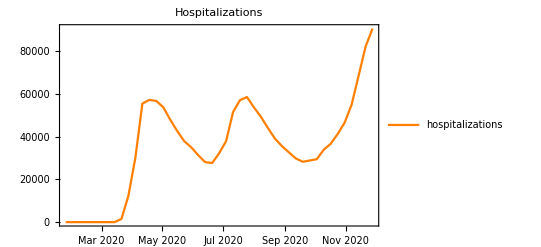

```mathematica
h = DateListPlot[finalDS[All, {"date", "hospitalizations"}], PlotLabel -> "Hospitalizations", PlotStyle -> Orange, PlotLegends -> {"hospitalizations"}]
```

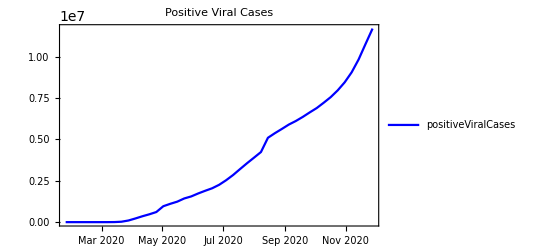

```mathematica
p = DateListPlot[finalDS[All, {"date", "positiveViralCases"}], PlotLabel -> "Positive Viral Cases", PlotStyle -> Blue, PlotLegends -> {"positiveViralCases"}]
```

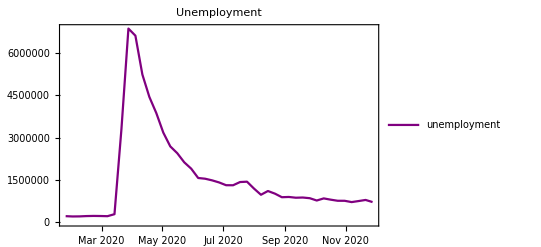

```mathematica
u = DateListPlot[finalDS[All, {"date", "ICSA"}], PlotLabel -> "Unemployment", PlotStyle -> Purple, PlotLegends  -> {"unemployment"}]
```

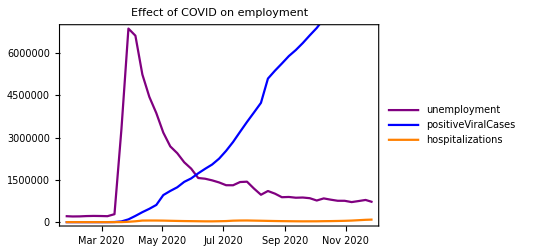

```mathematica
Show[u,p,h, PlotLabel -> "Effect of COVID on employment"] (*To combine 3 different graph onto one plot, I found the command "Show" from https://reference.wolfram.com/language/ref/Show.html*)
```